```mathematica
ClearAll["Global`*"]
```

```mathematica
a=0.2;
b=0.1;
```

```mathematica
f[t_]:={0.5+a Cos[2π t](1-Sin[2π t ]),0.5+ b Sin[2 π t](1+Cos[2 π t])}
```

```mathematica
λ[t_]:=NIntegrate[Norm[f'[s]],{s,0,t}]
```

```mathematica
(*1 test scalar*)
```

```mathematica
(*1.1 2d -> 1d *)
```

```mathematica
u01[x_]:=1+3 x[[1]]^2+2*x[[2]]^2
```

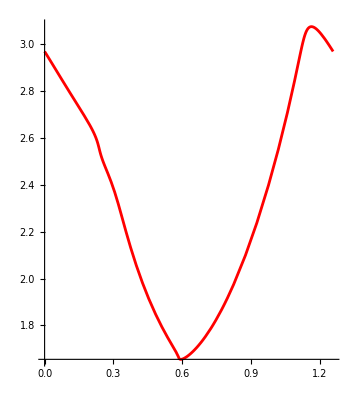

```mathematica
plotex=ParametricPlot[{λ[t],u01[f[t]]},{t,0,1},PlotStyle->Red]
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_1d.csv"];
t= Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

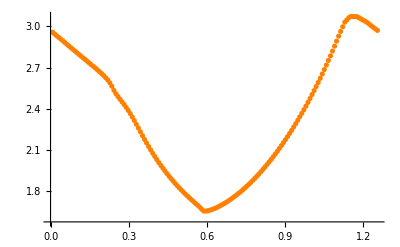

```mathematica
plotnum=ListPlot[t,PlotStyle->Orange]
```

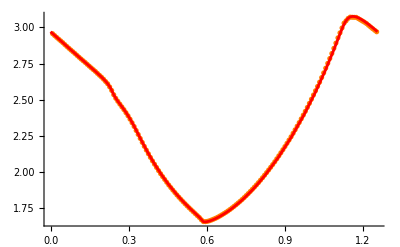

```mathematica
Show[plotnum,plotex,PlotRange->Full]
```

```mathematica
(*1 test vector*)
```

```mathematica
(*1.1 2d -> 1d *)
```

```mathematica
u01[x_]:={1-x[[1]]+2*x[[2]]^2,1-4x[[1]]^2+2 x[[2]]^2}
```

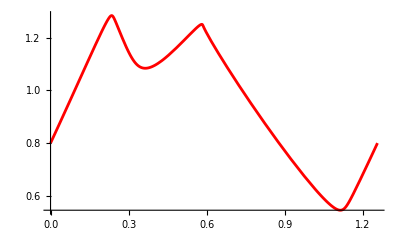
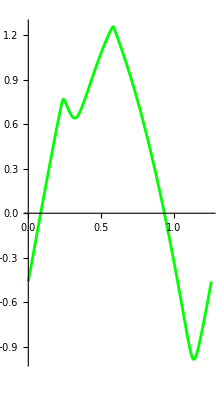

```mathematica
plotex={ParametricPlot[{λ[t],u01[f[t]][[1]]},{t,0,1},PlotStyle->Red],ParametricPlot[{λ[t],u01[f[t]][[2]]},{t,0,1},PlotStyle->Green]}
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/v_1d.csv"];
t= Table[{t[[i,3]],t[[i,1]],t[[i,2]]},{i,2,Length[t]}]
```

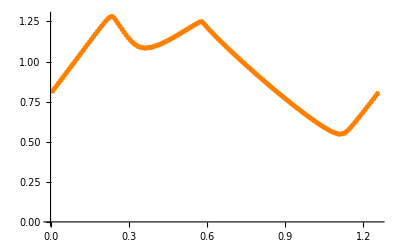
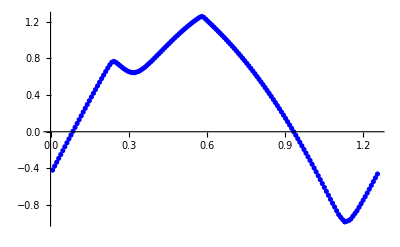

```mathematica
plotnum={ListPlot[Table[{t[[i,1]],t[[i,2]]},{i,1,Length[t]}],PlotStyle->Orange],ListPlot[Table[{t[[i,1]],t[[i,3]]},{i,1,Length[t]}],PlotStyle->Blue]}
```

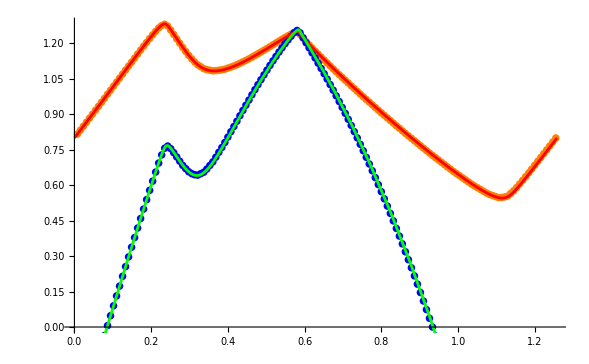

```mathematica
Show[plotnum,plotex]
```